# Calculation of adiabatic loading between harmonic potentials

### constants and units

```mathematica
μB=9.27400915*10^-28;
kb=1.380658*10^-23;
ℏ=6.62606896*10^-34(2π)^-1;
c=299792458;
a0 = .529*10^-10;
ϵ0 = 8.854*10^-12;
el = 1.602*10^-19;
AMU=1.66*10^-27*kg;
cm=10^-2;mm=10^-3;μm=10^-6;nm = 10^-9;pm=10^-12;fm=10^-15;
kg=1;g=10^-3;ng=10^-9*g;pg=10^-12*g;
Hz=1;kHz=10^3;MHz=10^6;GHz=10^9; THz = 10^12;
Kk=1;mK=10^-3;μK=10^-6;nK=10^-9;
Ww=1;mW=10^-3;μW=10^-6;nW=10^-9;
Pa=1;GPa=10^9;
ms=10^-3;
ohm=1;V=1;mV=10^-3;
ns = 10^-9;
```

```mathematica
mass = 1.44*10^-25;
```

## Parameters

#### potential parameters

```mathematica
waist1 =322nm;
(*waist2 = 322nm;*)
k = (2π)/(813nm);
pot1[x_] =-Exp[-(2 x^2)/waist1^2];
displacement = 100 nm;
pot2[x_] =-Cos[k*(x-displacement)]^2
```

-Cos[2000000000/813 π (-1/10000000+x)]^2

#### Simulation parameters: CAUTION: span/cutOff should be less than ground state oscillator size (<x3) if you want reliable numerics. *Confirmed that this ratio determines accuracy, consistent with expectation fro scaling to-π to π, and Fourier components on this range.

```mathematica
span = 0.6μm;(*should be at least the waist*)
cutOff=75 (*see above*)
span/cutOff//N
```

75

8.×10^-9

```mathematica
span/cutOff
```

8.×10^-9

```mathematica
.25/25
```

0.01

#### Ramp definitions

```mathematica
(*timeConst = .0001;*)
depth1=2π*1MHz;
A1[t_] = depth1*(1-Tanh[(t-2*timeConst)/timeConst])1/2
depth2=2π*1MHz;
A2[t_] = depth2*(1+Tanh[(t-2*timeConst)/timeConst])1/2
Hpot[t_,x_] =A1[t]*pot1[x]+A2[t]*pot2[x];
```

1000000 π (1-Tanh[(t-2 timeConst)/timeConst])

1000000 π (1+Tanh[(t-2 timeConst)/timeConst])

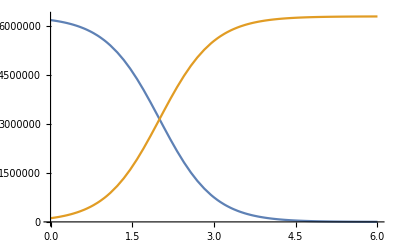

```mathematica
Plot[{A1[t]/.timeConst-> 1,A2[t]/.timeConst-> 1},{t,0,6}, FrameLabel-> {"time (s)", "depth"}]
```

```mathematica
Manipulate[Plot[Hpot[t,x]/.timeConst-> .0002, {x,-1μm,1μm}],{t,0,1ms}]
```

```mathematica
hilbDim
```

hilbDim

## Hamiltonian: all in Hz - Let ℏ = 1,

#### Ramp definitions

#### Continuous space

```mathematica
Hpot[t_,x_] =A1[t]*pot1[x]+A2[t]*pot2[x];
```

```mathematica
Hpot[0.1,x]
```

-1000000 ⅇ^(-(500000000000000000 x^2)/25921) π (1-Tanh[(0.1-2 timeConst)/timeConst])-1000000 π Cos[2000000000/813 π (-1/10000000+x)]^2 (1+Tanh[(0.1-2 timeConst)/timeConst])

```mathematica
P0=Plot[Hpot[0,x],{x,-span/2,span/2},PlotStyle->{Thick,Blue},Frame->True,PlotRange->{-2depth1,0}];
scale=π/span;
```

```mathematica
waist1Scaled=scale*waist1;
kscaled = scale^-1*k;
displacementScaled = scale*displacement;
```

```mathematica
pot1Scaled[x_] =-Exp[-(2 x^2)/waist1Scaled^2];
pot2Scaled[x_] =-Cos[kscaled*(x-displacementScaled)]^2;
```

```mathematica
potentialScaled[t_,x_] = A1[t]*pot1Scaled[x]+A2[t]*pot2Scaled[x];
```

```mathematica
(*FA[t_,x_]=FourierSeries[potentialScaled[t,x],x,cutOff];*)
(*FA[t_,x_]=Sum[Integrate[Chop[1/(2π)potentialScaled[t,xx]]*Exp[ii*I* xx],{xx,-π,π}]Exp[-ii*I* x],{ii,-cutOff,cutOff,1}];*)
P1=Plot[potentialScaled[0,x],{x,-π,π},PlotStyle->{Thick,Blue}];
P2=Plot[FA[t,x],{x,-π,π},PlotStyle->{Red,Thick,Dotted}, PlotRange-> All];

FAscaled[t_,x_]=FA[t,scale*x];
P3=Plot[FAscaled[0,x],{x,-span/2,span/2},PlotStyle->{Thick,Red,Dotted},Frame->True,PlotRange->{-2depth1,0}];
```

#### Hamiltonian

```mathematica
(*coefflist=Delete[Table[If[ii≠0,Coefficient[Chop[FA[t,xx]],Exp[I*ii *xx]],0],{ii,-cutOff,cutOff}],cutOff+1];*)(*delete zero frequency term*)
```

```mathematica
(*coefflist1=Delete[Table[If[ii≠0,NIntegrate[Chop[1/(2π)pot1Scaled[xx]]*Exp[ii*I* xx],{xx,-π,π}],0],{ii,-cutOff,cutOff}],cutOff+1];
coefflist2=Delete[Table[If[ii≠0,NIntegrate[Chop[1/(2π)pot2Scaled[xx]]*Exp[ii*I* xx],{xx,-π,π}],0],{ii,-cutOff,cutOff}],cutOff+1];*)
```

```mathematica
coefflist1=Table[NIntegrate[Chop[1/(2π)pot1Scaled[xx]]*Exp[ii*I* xx],{xx,-π,π}],{ii,-cutOff,cutOff}];
coefflist2=Table[NIntegrate[Chop[1/(2π)pot2Scaled[xx]]*Exp[ii*I* xx],{xx,-π,π}],{ii,-cutOff,cutOff}];
```

```mathematica
(*indexFunction[delta_] = If[delta<0, delta+cutOff+1,delta+cutOff]*)
```

```mathematica
indexFunction[delta_] =  delta+cutOff+1;
```

```mathematica
(*This basis is - (cut off-1)/2 to (cut off-1)/2, no zero frequency*)
```

```mathematica
1+cutOff+1
```

77

```mathematica
((cutOff+1)/2-i)/.i-> cutOff-1
```

-36

```mathematica
cutOff
```

75

```mathematica
ham1  =ConstantArray[0,{cutOff,cutOff}];
Do[
ham1[[i,j]]=If[i==j,1/(2ℏ)ℏ^2/(2*mass)((2π)/(2span))^2((cutOff+1)/2-i)^2,A1[t]*coefflist1[[indexFunction[j-i]]]]
,
{i,1,(cutOff)},{j,1,(cutOff)}]
ham2  =ConstantArray[0,{cutOff,cutOff}];
Do[
ham2[[i,j]]=If[i==j,1/(2ℏ)ℏ^2/(2*mass)((2π)/(2span))^2((cutOff+1)/2-i)^2,A2[t]*coefflist2[[indexFunction[j-i]]]]
,
{i,1,(cutOff)},{j,1,(cutOff)}]
```

```mathematica
H[t_] = ham1+ham2;
```

```mathematica
(*Hinit[t_] =ham1+ham2;*)
```

```mathematica
(*Hinit1[t_]=Delete[Hinit[t],(cutOff-1)/2+1];
H[t_]=Transpose[Delete[Transpose[Hinit1[t]],(cutOff-1)/2+1]];*)
```

```mathematica
test = Chop[SetPrecision[H[0],12]];
```

```mathematica
(*test = Chop[SetPrecision[H[0],12]];
Do[
If[test[[i,j]]≠ Conjugate[test[[j,i]]], Print[i," ",j]]
,{i,1,Length[H[0]]},{j,1,Length[H[0]]}]*)
```

```mathematica
(Conjugate[Transpose[H[.1]]]==H[.1])/.timeConst-> .01
```

True

#### Check on Fouriering: in this case there is no halving of the frequency since we are using coeff list, not the basis (which only goes from -cutoff-1/2 to +

```mathematica
reconstrPot[x_] = Sum[If[ii≠0,Exp[-I*ii*x]coefflist1[[indexFunction[ii]]],0],{ii,-cutOff,cutOff}];
```

```mathematica
reconstrPot[x_] = Sum[Exp[-I*ii*x]coefflist1[[indexFunction[ii]]],{ii,-cutOff,cutOff}];
```

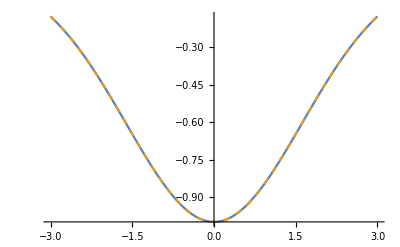

```mathematica
Plot[{reconstrPot[scale*x],pot1[x]},{x,-span/2,span/2} , PlotStyle-> {Solid, Dashed}] (*there's an offset but that shouldn't matter*)
```

```mathematica
reconstrPot[x_] = Sum[If[ii≠0,Exp[-I*ii*x]coefflist2[[indexFunction[ii]]],0],{ii,-cutOff,cutOff}];
```

```mathematica
reconstrPot[x_] = Sum[Exp[-I*ii*x]coefflist2[[indexFunction[ii]]],{ii,-cutOff,cutOff}];
```

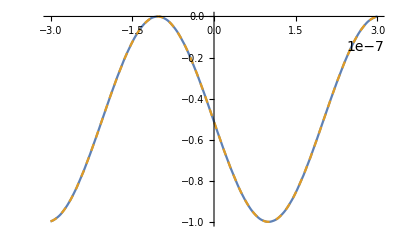

```mathematica
Plot[{reconstrPot[scale*x],pot2[x]},{x,-span/2,span/2} ,PlotStyle-> {Solid, Dashed}] (*there's an offset again but that really shouldn't matter*)
```

## Dynamics

#### Ramp time scale

```mathematica
timeConst = .00005
```

0.00005

#### Compute trap frequencies

```mathematica
A1[0]
```

6.17017×10^6

```mathematica
depth1//N
```

6.28319×10^6

```mathematica
trapFreq1 = (2SeriesCoefficient[ℏ*A1[0]*pot1[x], {x,0,2}]/mass)^(1/2)
trapFreq2 = (2SeriesCoefficient[ℏ*A2[4*timeConst]*pot2[x], {x,displacement,2}]/mass)^(1/2)
```

417522.

734700.

```mathematica
2π*((2*ℏ*A2[4*timeConst])/(mass*(813nm)^2))^(1/2)
```

734700.

```mathematica
(trapFreq1/(2π))^-1
```

0.0000150487

```mathematica
x01 = (ℏ/(2*mass*trapFreq1))^(1/2);
x02 = (ℏ/(2*mass*trapFreq2))^(1/2);
```

#### Find initial ground state: this shoudl be gaussian, come back to this.

```mathematica
584793/417522.27175560175//N
```

1.40063

```mathematica
2^(1/2)//N
```

1.41421

```mathematica
sorted = Sort[Transpose[SetPrecision[Eigensystem[H[0]],8]]];
```

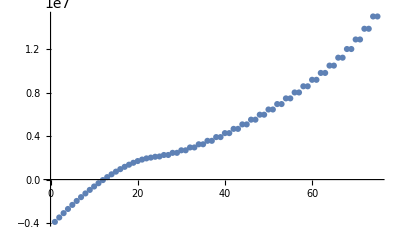

```mathematica
ListPlot[Transpose[sorted][[1]]]
```

```mathematica
gs = sorted[[1,2]];
```

```mathematica
ψin = gs;
```

#### Splittings here should match analytic result: within 4%. The factor of 2 in the diagonals is required to get this right.

```mathematica
Transpose[sorted][[1]][[1]]-Transpose[sorted][[1]][[2]]
```

-407560.

```mathematica
Transpose[sorted][[1]][[2]]-Transpose[sorted][[1]][[3]]
```

-396622.

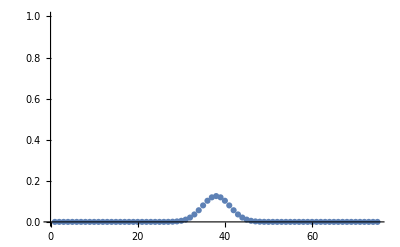

```mathematica
ListPlot[Map[Norm[#]^2&,ψin], PlotRange-> {0,1}]
```

```mathematica
Length[ψin]
```

75

```mathematica
freq = Table[ii-(cutOff+1)/2,{ii,1,(cutOff)}];
```

```mathematica
freq = Join[Reverse[ Table[-ii,{ii,1,((cutOff-1)/2)}]], {0},Table[ii,{ii,1,((cutOff-1)/2)}]];
```

```mathematica
freq[[55]]
```

17

```mathematica
27*2
```

54

```mathematica
freq[[cutOff-1]]
```

36

#### Note the flipped sign in teh exponential from what you’d expect is from teh ordering of the hamiltonian above. Starts with negative frequencies.

```mathematica
realSpaceGS[x_] = Sum[ψin[[ii]]*Exp[-I*freq[[ii]]*x*scale],{ii,1,cutOff}];
```

```mathematica
norm =( NIntegrate[Conjugate[realSpaceGS[x]]realSpaceGS[x],{x,-span/2,span/2} ])^(1/2);
```

```mathematica
realSpaceGSNorm[x_]= 1/norm realSpaceGS[x];
```

```mathematica
gaussNorm = NIntegrate[Exp[(-(x)^2)/(2*(x01)^2)],{x,-span/2,span/2}];
waveFunc1[x_] =1/(gaussNorm)^(1/2) Exp[(-(x)^2)/(4*(x01)^2)];
```

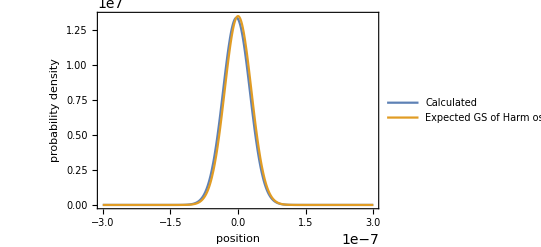

```mathematica
Plot[{Norm[realSpaceGSNorm[x]]^2,waveFunc1[x]^2},{x,-span/2,span/2}, PlotRange-> {0,All}, Frame-> True, Axes-> False, FrameLabel-> {"position","probability density"}, PlotLegends-> {"Calculated","Expected GS of Harm oscillator"}]
```

```mathematica
(*Note the slight offset to the right is from the potential 2 turning on in the beginning a tiny amount. The height difference I am unsure the cause of*)
```

#### Schrodinger evolution

```mathematica
t
```

t

```mathematica
Clear[j,ψ,g,t,ψsolved];
ψ[t_] =Table[cf[j][t],{j,1,cutOff}];
(*tFinal = 200*timeConst;*)
```

```mathematica
tFinal = 4*timeConst;
```

```mathematica
LHS =H[t].ψ[t];
RHS = I*D[ψ[t],t];
LHSin = ψ[0];
RHSin = Chop[ψin];
eqns=MapThread[#1==#2&,{LHS,RHS}];
eqnsIn = MapThread[#1==#2&,{LHSin,RHSin}];
solEqns = Join[eqns,eqnsIn];
solns = NDSolve[solEqns, ψ[t],{t,0,tFinal}];
ψsolved[t_] = ψ[t]/.solns[[1]];
```

```mathematica
probDist = Map[Norm[#]^2&,ψsolved[t]];
```

```mathematica
(*Manipulate[ListPlot[probDist/.t-> t0, PlotRange-> {0,1}],{t0,0,tFinal}]*)
```

```mathematica
Total[probDist/.t-> .00001]
```

0.999996

```mathematica
sorted = Sort[Transpose[SetPrecision[Eigensystem[H[tFinal]],8]]];
```

```mathematica
gsFinal = sorted[[1,2]];
```

```mathematica
Norm[gsFinal]
```

1.

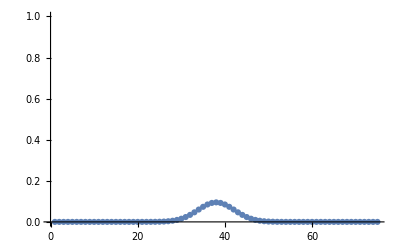

```mathematica
ListPlot[Map[Norm[#]^2&,gsFinal], PlotRange-> {0,1}]
```

```mathematica
overlapFinalGS[t_] =Norm[Conjugate[ψsolved[t]].gsFinal]^2;
```

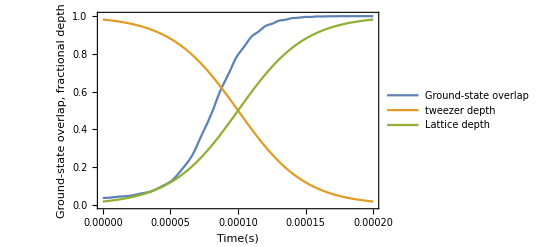

```mathematica
Plot[{overlapFinalGS[t],A1[t]/depth1,A2[t]/depth2},{t,0,tFinal},PlotRange-> {0,1},Frame-> True, Axes-> False, FrameLabel-> {"Time(s)","Ground-state overlap, fractional depth","tanh ramp with time constant = " <> ToString[timeConst/ms]<>" ms, with " <> ToString[displacement/nm]<>"nm initial displacement",}, LabelStyle-> Black, PlotLegends-> {"Ground-state overlap","tweezer depth","Lattice depth"}]
```

```mathematica
aaa
```

```mathematica
overlapFinalGS[tFinal]
```

0.992527

```mathematica
overlapFinalGS[0]
```

0.037427

```mathematica
Conjugate[gsFinal].gs
```

-0.0244395-0.3141219 ⅈ

```mathematica
Norm[Conjugate[gsFinal].gs]^2
```

0.0992699

```mathematica
Clear[waveFunc]
```

```mathematica
gaussNorm = NIntegrate[Exp[(-(x-displacement)^2)/(2*(x02)^2)],{x,-span/2,span/2}]
waveFunc[x_] =1/(gaussNorm)^(1/2) Exp[(-(x-displacement)^2)/(4*(x02)^2)]
```

5.59599×10^-8

4227.29 ⅇ^(-5.0161×10^14 (-1/10000000+x)^2)

```mathematica
NIntegrate[waveFunc1[x]*waveFunc[x]  ,{x,-span/2,span/2}]^2(*disparity here is present out to large span/cutoff, tried 0.7 um and 131 cutoff, so I don't thin kthat's the problem*)
```

0.0253571

```mathematica
Norm[Conjugate[ψsolved[0]].ψsolved[tFinal]]^2
```

0.0377265

```mathematica
realSpaceGSFinal[x_] = Sum[If[ii≠ (cutOff+1)/2,ψsolved[tFinal][[ii]]*Exp[I*freq[[ii]]*x*scale],0],{ii,1,cutOff}];
normFinal =( NIntegrate[Conjugate[realSpaceGSFinal[x]]realSpaceGSFinal[x],{x,-span/2,span/2} ])^(1/2);
realSpaceGSFinalNorm[x_] =1/normFinal realSpaceGSFinal[x];
```

```mathematica
diagonlizedGS[x_] = Sum[If[ii≠ (cutOff+1)/2,gsFinal[[ii]]*Exp[I*freq[[ii]]*x*scale],0],{ii,1,cutOff}];
normFinal =( NIntegrate[Conjugate[diagonlizedGS[x]]diagonlizedGS[x],{x,-span/2,span/2} ])^(1/2)
diagonlizedGSNorm[x_] =1/normFinal diagonlizedGS[x];
```

0.00101436+4.60548×10^-22 ⅈ

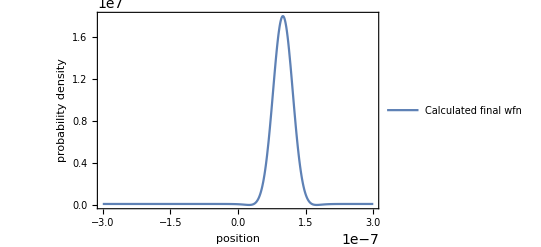

```mathematica
Plot[{Norm[diagonlizedGSNorm[x]]^2},{x,-span/2,span/2}, PlotRange-> All, Frame-> True, Axes-> False, FrameLabel-> {"position","probability density"}, PlotLegends-> {"Calculated final wfn","Expected GS of Harm oscillator in right tweezer"}]
```

```mathematica
Norm[NIntegrate[Conjugate[realSpaceGSFinalNorm[x]]*diagonlizedGSNorm[x]  ,{x,-span/2,span/2}]]^2
```

0.999956

```mathematica
diagonlizedGSNorm[1*10^-7]
```

2482.05+3432.96 ⅈ

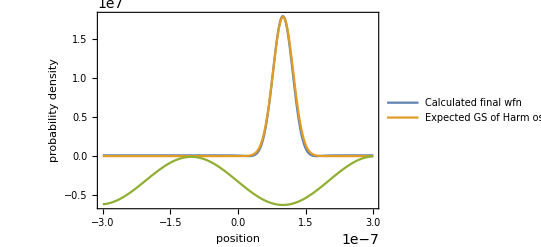

```mathematica
Plot[{Norm[realSpaceGSFinalNorm[x]]^2,(waveFunc[x])^2, Hpot[tFinal,x]},{x,-span/2,span/2}, PlotRange-> All, Frame-> True, Axes-> False, FrameLabel-> {"position","probability density"}, PlotLegends-> {"Calculated final wfn","Expected GS of Harm oscillator in right tweezer"}]
```

```mathematica
Clear[realSpaceGSFinalDynNorm]
```

```mathematica
realSpaceGSFinalDyn[x_,t_] = Sum[If[ii≠ (cutOff+1)/2,ψsolved[t][[ii]]*Exp[I*freq[[ii]]*x*scale],0],{ii,1,cutOff}];
normFinalDyn =( NIntegrate[Conjugate[realSpaceGSFinalDyn[x,0]]realSpaceGSFinalDyn[x,0],{x,-span/2,span/2} ])^(1/2);
realSpaceGSFinalDynNorm[x_,t_]= 1/normFinal realSpaceGSFinalDyn[x,t];
```

```mathematica
Manipulate[Plot[{Norm[realSpaceGSFinalDynNorm[x,t0]]^2,(waveFunc[x])^2},{x,-span/2,span/2}, PlotRange-> {0,All}, Frame-> True, Axes-> False, FrameLabel-> {"position","probability density"}, PlotLegends-> {"Calculated final wfn","Expected GS of Harm oscillator in right tweezer"}],{t0,0,tFinal}]
```

Plot::plln: Limiting value -span/2 in {x,-span/2,span/2} is not a machine-sized real number.

```mathematica
indexFunction[delta_] = If[delta<0, delta+cutOff+1,delta+cutOff]
```

If[delta<0,delta+cutOff+1,delta+cutOff]

```mathematica
cutOff
```

101

```mathematica
indexFunction[-cutOff]
```

1

## Random scratch work

```mathematica
(.61)/(.68)*515*.7
```

323.39

```mathematica
x
```

x

```mathematica
Clear[x]
```

```mathematica
waist
```

waist

```mathematica
NA = 0.62;
waist = (.61)/NA*.515*.7;
tweezerPot[x_,x0_] =- Exp[-2*(x-x0)^2/(waist^2)];
latticePot[x_] = -Cos[2(2π)/(.813)x]^2;
sumPot[x_,x0_] = tweezerPot[x,x0] +latticePot[x];
Manipulate[Plot[sumPot[x,x0],{x,0,1} ],{x0,0,1}]
```

```mathematica
NA = 0.68;
waist = (.61)/NA*.515*.7
```

0.32339

```mathematica
119-97.5
```

21.5

```mathematica
69-97.5
```

-28.5

```mathematica
50/400//N
```

0.125

```mathematica
Solve[400 == θ*π*(.0075)/(852*10^-9),θ]
```

{{θ→0.014464}}

```mathematica
.209*30
```

6.27

```mathematica
.209*10^-6/(20*10^-3)*20*30
```

0.00627

```mathematica
400==θ*π*633/(2000000 π θ)/(850*10^-9)
```

False

```mathematica
Solve[500==θ*π*ω0/(633*10^-9),ω0]
```

{{ω0→633/(2000000 π θ)}}

```mathematica
(500*633*10^-9)/(π*.00335)
```

0.0300732

```mathematica
.006*π*.001/(850*10^-9)
```

22.1759

```mathematica
(400*850*10^-9)/(π*.00325)
```

0.0333001

```mathematica
waist/.4065
```

0.795547

```mathematica
NA = 0.68;
waist = (.61)/NA*.795*.7
```

0.499213

```mathematica
waist = (.61)/(.83)*.649*.7
```

0.333883

```mathematica
waist/.532
```

0.6276

```mathematica
408/680//N
```

0.6

```mathematica
tweezerNumber = 10;
```

```mathematica
NA = 0.68
waist = (.61)/NA*.515*.7
tweezerArray[x_,x0_,spacing_] =Sum[- Exp[-2*(x-x0-ii*spacing)^2/(waist^2)],{ii,0,tweezerNumber-1}];
latticePot[x_] = -Cos[(2π)/(.813)x]^2;
sumPot[x_,x0_,spacing_] = tweezerArray[x,x0,spacing] +latticePot[x];
Manipulate[Plot[{sumPot[x,x0,spacing],latticePot[x],tweezerArray[x,x0,spacing]},{x,-1,10} ],{x0,0,1},{spacing,0,1}]
```

0.68

0.32339

```mathematica
(100/70)^(1/2)//N
```

1.19523

```mathematica
(65/55)//N
```

1.18182

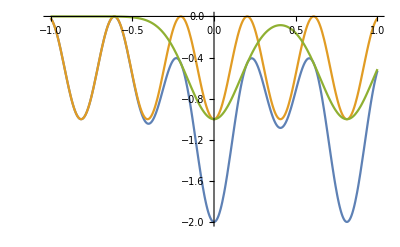

```mathematica
Plot[{sumPot[x,0,.813],latticePot[x],tweezerArray[x,0,.813]},{x,-1,1} ]
```

```mathematica
sumPot[x,x0,1]
```

-ⅇ^(-19.124 (-9+x-x0)^2)-ⅇ^(-19.124 (-8+x-x0)^2)-ⅇ^(-19.124 (-7+x-x0)^2)-ⅇ^(-19.124 (-6+x-x0)^2)-ⅇ^(-19.124 (-5+x-x0)^2)-ⅇ^(-19.124 (-4+x-x0)^2)-ⅇ^(-19.124 (-3+x-x0)^2)-ⅇ^(-19.124 (-2+x-x0)^2)-ⅇ^(-19.124 (-1+x-x0)^2)-ⅇ^(-19.124 (x-x0)^2)-Cos[7.7284 x]^2